```mathematica
geom={{15.5,0.65,c},{13.5,1.65,c},{0.0,2.05,c},{-13.5,1.65,c},{-15.5,0.65,c},{-9.5,-2.35,c},{0,-2.35,c},{9.5,-2.35,c},{15.5,0.65,c}}[[All,1;;2]]
```

{{15.5,0.65},{13.5,1.65},{0.,2.05},{-13.5,1.65},{-15.5,0.65},{-9.5,-2.35},{0,-2.35},{9.5,-2.35},{15.5,0.65}}

```mathematica
arcgen[{p1_,p2_,p3_},r_,n_]:=Module[{dc=Normalize[p1-p2]+Normalize[p3-p2],cc,th,ie,det},
If[EuclideanDistance[dc,Projection[dc,p1-p2]]<10^-3,ie=0,ie=1/EuclideanDistance[dc,Projection[dc,p1-p2]]];
cc=p2+r dc*ie;
If[ie==0,det=0,det=Det[PadRight[{p1,p2,p3},{3,3},1]]];
th=Sign[det] (π-VectorAngle[p3-p2,p1-p2])/(n-1);(*при обходе против часовой стрелке sign = 1*)
NestList[RotationTransform[th,cc],p2+Projection[cc-p2,p1-p2],n-1]]
roundedPolygon[Polygon[opts_?MatrixQ],r_?NumericQ,n:(_Integer?Positive):12]:=With[{pts=Split[opts][[All,1]]},Polygon[Flatten[arcgen[#,r,n]&/@Partition[If[TrueQ[First[pts]==Last[pts]],Most,Identity][pts],3,1,{2,-2}],1]]];
```

```mathematica
Partition[If[TrueQ[First[pts]==Last[pts]],Most,Identity][pts],3,1,{2,-2}]
```

{{{9.5,-2.35},{15.5,0.65},{13.5,1.65}},{{15.5,0.65},{13.5,1.65},{0.,2.05}},{{13.5,1.65},{0.,2.05},{-13.5,1.65}},{{0.,2.05},{-13.5,1.65},{-15.5,0.65}},{{-13.5,1.65},{-15.5,0.65},{-9.5,-2.35}},{{-15.5,0.65},{-9.5,-2.35},{0,-2.35}},{{-9.5,-2.35},{0,-2.35},{9.5,-2.35}},{{0,-2.35},{9.5,-2.35},{15.5,0.65}}}

```mathematica
{p1,p2,p3}={{9.5,-2.35},{15.5,0.65},{13.5,1.65}};
```

```mathematica
PadRight[{p1,p2,p3},{3,3},1]//MatrixForm
```

(9.5 | -2.35 | 1
15.5 | 0.65 | 1
13.5 | 1.65 | 1)

```mathematica
VectorAngle[p3-p2,p1-p2]
```

0.927295

```mathematica
Det[PadRight[{p1,p2,p3},{3,3},1]]
```

12.

```mathematica
cc=p2+0.1 (Normalize[p1-p2]+Normalize[p3-p2])1/EuclideanDistance[Normalize[p1-p2]+Normalize[p3-p2],Projection[Normalize[p1-p2]+Normalize[p3-p2],p1-p2]]
```

{15.2764,0.65}

```mathematica
NestList[RotationTransform[(π-VectorAngle[p3-p2,p1-p2])/11,cc],p2+Projection[cc-p2,p1-p2],11]
```

{{15.3211,0.560557},{15.3381,0.571305},{15.3526,0.585231},{15.364,0.601773},{15.3719,0.620262},{15.3759,0.639952},{15.3759,0.660048},{15.3719,0.679738},{15.364,0.698227},{15.3526,0.714769},{15.3381,0.728695},{15.3211,0.739443}}

```mathematica
pts=geom[[1;;-1]];
pol=Polygon[pts];
ListAnimate[Table[Graphics[{EdgeForm[Thick],White,roundedPolygon[pol,r]}],{r,.01,4,.01}]]
```

{{15.3211,0.560557},{15.3381,0.571305},{15.3526,0.585231},{15.364,0.601773},{15.3719,0.620262},{15.3759,0.639952},{15.3759,0.660048},{15.3719,0.679738},{15.364,0.698227},{15.3526,0.714769},{15.3381,0.728695},{15.3211,0.739443},{13.5197,1.64014},{13.5162,1.64183},{13.5125,1.64339},{13.5088,1.6448},{13.5051,1.64606},{13.5013,1.64717},{13.4975,1.64813},{13.4936,1.64895},{13.4897,1.6496},{13.4858,1.65011},{13.4819,1.65046},{13.478,1.65065},{0.00296166,2.04991},{0.0024233,2.04993},{0.00188486,2.04994},{0.00134637,2.04995},{0.000807836,2.04995},{0.000269281,2.04996},{-0.000269281,2.04996},{-0.000807836,2.04995},{-0.00134637,2.04995},{-0.00188486,2.04994},{-0.0024233,2.04993},{-0.00296166,2.04991},{-13.478,1.65065},{-13.4819,1.65046},{-13.4858,1.65011},{-13.4897,1.6496},{-13.4936,1.64895},{-13.4975,1.64813},{-13.5013,1.64717},{-13.5051,1.64606},{-13.5088,1.6448},{-13.5125,1.64339},{-13.5162,1.64183},{-13.5197,1.64014},{-15.3211,0.739443},{-15.3381,0.728695},{-15.3526,0.714769},{-15.364,0.698227},{-15.3719,0.679738},{-15.3759,0.660048},{-15.3759,0.639952},{-15.3719,0.620262},{-15.364,0.601773},{-15.3526,0.585231},{-15.3381,0.571305},{-15.3211,0.560557},{-9.52111,-2.33944},{-9.51731,-2.34125},{-9.51342,-2.34289},{-9.50948,-2.34437},{-9.50547,-2.34568},{-9.50141,-2.34682},{-9.49731,-2.34779},{-9.49317,-2.34858},{-9.489,-2.3492},{-9.48481,-2.34964},{-9.48061,-2.34991},{-9.47639,-2.35},{0.,-2.35},{0.,-2.35},{0.,-2.35},{0.,-2.35},{0.,-2.35},{0.,-2.35},{0.,-2.35},{0.,-2.35},{0.,-2.35},{0.,-2.35},{0.,-2.35},{0.,-2.35},{9.47639,-2.35},{9.48061,-2.34991},{9.48481,-2.34964},{9.489,-2.3492},{9.49317,-2.34858},{9.49731,-2.34779},{9.50141,-2.34682},{9.50547,-2.34568},{9.50948,-2.34437},{9.51342,-2.34289},{9.51731,-2.34125},{9.52111,-2.33944}}

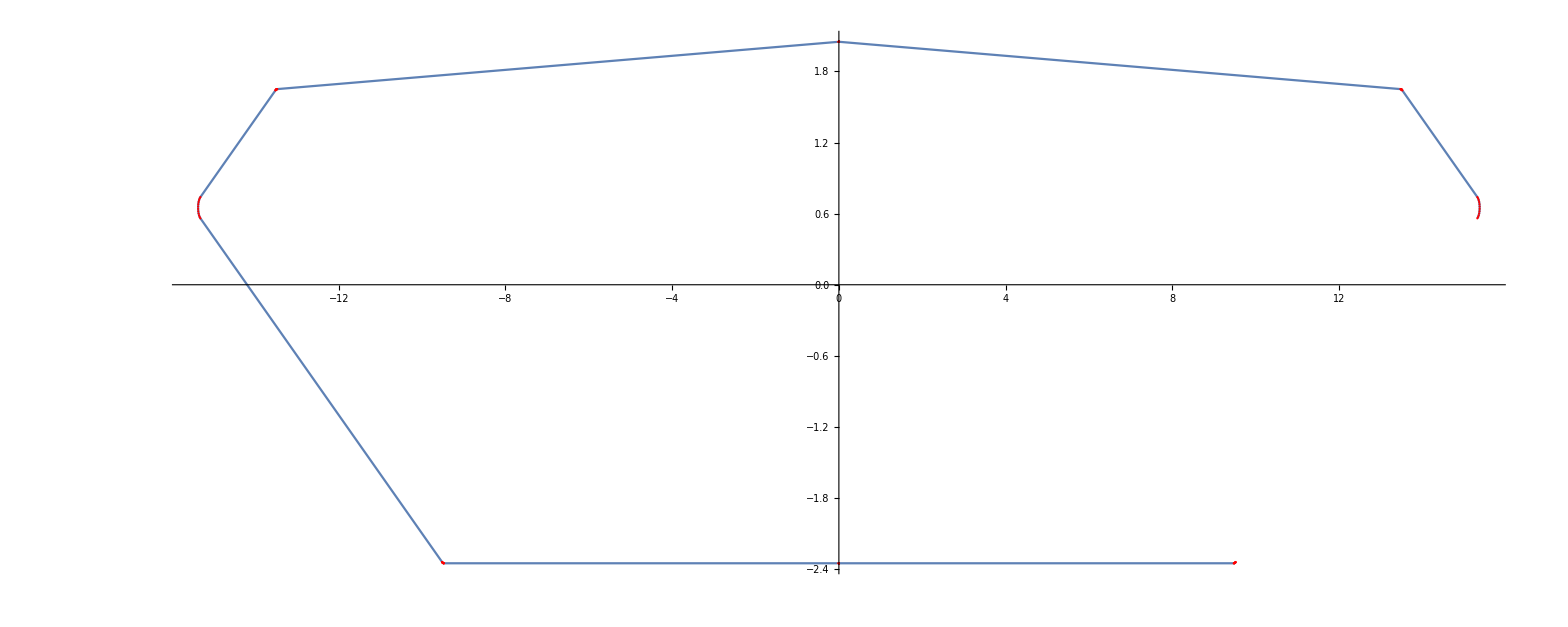

```mathematica
pp=roundedPolygon[pol,0.1][[1]]
ListLinePlot[pp,AspectRatio->Automatic,Mesh->All,MeshStyle->Directive[Red,PointSize->0.001]]
```

```mathematica
{#[[1]],#[[2]],i}&/@pp
```

{{15.3211,0.560557,i},{15.3381,0.571305,i},{15.3526,0.585231,i},{15.364,0.601773,i},{15.3719,0.620262,i},{15.3759,0.639952,i},{15.3759,0.660048,i},{15.3719,0.679738,i},{15.364,0.698227,i},{15.3526,0.714769,i},{15.3381,0.728695,i},{15.3211,0.739443,i},{13.5197,1.64014,i},{13.5162,1.64183,i},{13.5125,1.64339,i},{13.5088,1.6448,i},{13.5051,1.64606,i},{13.5013,1.64717,i},{13.4975,1.64813,i},{13.4936,1.64895,i},{13.4897,1.6496,i},{13.4858,1.65011,i},{13.4819,1.65046,i},{13.478,1.65065,i},{0.00296166,2.04991,i},{0.0024233,2.04993,i},{0.00188486,2.04994,i},{0.00134637,2.04995,i},{0.000807836,2.04995,i},{0.000269281,2.04996,i},{-0.000269281,2.04996,i},{-0.000807836,2.04995,i},{-0.00134637,2.04995,i},{-0.00188486,2.04994,i},{-0.0024233,2.04993,i},{-0.00296166,2.04991,i},{-13.478,1.65065,i},{-13.4819,1.65046,i},{-13.4858,1.65011,i},{-13.4897,1.6496,i},{-13.4936,1.64895,i},{-13.4975,1.64813,i},{-13.5013,1.64717,i},{-13.5051,1.64606,i},{-13.5088,1.6448,i},{-13.5125,1.64339,i},{-13.5162,1.64183,i},{-13.5197,1.64014,i},{-15.3211,0.739443,i},{-15.3381,0.728695,i},{-15.3526,0.714769,i},{-15.364,0.698227,i},{-15.3719,0.679738,i},{-15.3759,0.660048,i},{-15.3759,0.639952,i},{-15.3719,0.620262,i},{-15.364,0.601773,i},{-15.3526,0.585231,i},{-15.3381,0.571305,i},{-15.3211,0.560557,i},{-9.52111,-2.33944,i},{-9.51731,-2.34125,i},{-9.51342,-2.34289,i},{-9.50948,-2.34437,i},{-9.50547,-2.34568,i},{-9.50141,-2.34682,i},{-9.49731,-2.34779,i},{-9.49317,-2.34858,i},{-9.489,-2.3492,i},{-9.48481,-2.34964,i},{-9.48061,-2.34991,i},{-9.47639,-2.35,i},{0.,-2.35,i},{0.,-2.35,i},{0.,-2.35,i},{0.,-2.35,i},{0.,-2.35,i},{0.,-2.35,i},{0.,-2.35,i},{0.,-2.35,i},{0.,-2.35,i},{0.,-2.35,i},{0.,-2.35,i},{0.,-2.35,i},{9.47639,-2.35,i},{9.48061,-2.34991,i},{9.48481,-2.34964,i},{9.489,-2.3492,i},{9.49317,-2.34858,i},{9.49731,-2.34779,i},{9.50141,-2.34682,i},{9.50547,-2.34568,i},{9.50948,-2.34437,i},{9.51342,-2.34289,i},{9.51731,-2.34125,i},{9.52111,-2.33944,i}}